```mathematica
RungeKutta Method 4th
```

```mathematica
$HistoryLength=3;
ClearAll[SOL,Xinit,Yinit,Pxinit,Pyinit];
Needs["DifferentialEquations`NDSolveProblems`"];
Timing[
R=0.08;(*Radius of solenoid coil[m]*)
l=0.3;(*Lenght of solenoid coil[m]*)
Lz=20;(*Simulation area of longitudinal direction[m]*)
clight=2.99792458*10^8;(*Speed of light[m/s]*)
m=238*1.66053892*10^-27;(*Mass of ion[kg]*)
q=1.60217657*10^-19;(*Elementary chrge*)
Inum=34;
Ene=3*10^6;(*Kinetic energy*)
γ=q*Ene/(m*clight^2)+1;(*Lorentz factor*)
v=clight √(1-1/γ^2);(*Velosity of ion*)
Bz0=1.8184449309034985;(*Need to scale magnetic fields*)
Xinit[1]={0.002,0.004};(*Initial x coodinate[m]*)
Yinit[1]={0.002,0};(*Initial y coodinate[m]*)
Pxinit[1]={100,0};(*Initial vx[m/s]*)
Pyinit[1]={100,100};(*Initial vy[m/s]*)
Br[r_,z_]:=NIntegrate[1/(2π)*((R*Cos[θ])/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(R*Cos[θ])/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ])))/Bz0,{θ,0,2π}];(*Br not scaled*)
Bz[r_,z_]:=NIntegrate[1/(2π)((R^2-R*r*Cos[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ])))/Bz0,{θ,0,2π}];(*Bz not scaled*)

Vari={x,y,z};(*Variable of equation*)
Time={t,0,Lz/v};(*Simulation time*)
Table[Eqs[i]={m*γ*x''[t]==Inum*q*(y'[t]*Bz[√(x[t]^2+y[t]^2),z[t]]-z'[t]*y[t]/(√(x[t]^2+y[t]^2))*Br[√(x[t]^2+y[t]^2),z[t]]),m*γ*y''[t]==Inum*q*(z'[t]*x[t]/(√(x[t]^2+y[t]^2))*Br[√(x[t]^2+y[t]^2),z[t]]-x'[t]*Bz[√(x[t]^2+y[t]^2),z[t]]),m*γ*z''[t]==Inum*q*(x'[t]*y[t]/(√(x[t]^2+y[t]^2))*Br[√(x[t]^2+y[t]^2),z[t]]-y'[t] x[t]/(√(x[t]^2+y[t]^2))*Br[√(x[t]^2+y[t]^2),z[t]]),x[0]==Xinit[1][[i]],x'[0]==Pxinit[1][[i]],y[0]==Yinit[1][[i]],y'[0]==Pyinit[1][[i]],z[0]==-Lz/2,z'[0]==v},{i,1,2}];
(*Equation of motion*)

Table[SOL[i]=NDSolveValue[Eqs[i],Vari,Time,Method->{"ExplicitRungeKutta","DifferenceOrder"->4}, MaxSteps->10^5],{i,1,2}];(*Solve equation of motion numerically*)
]
```

{56.4538,Null}

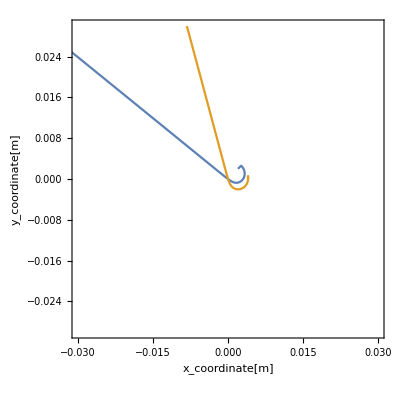

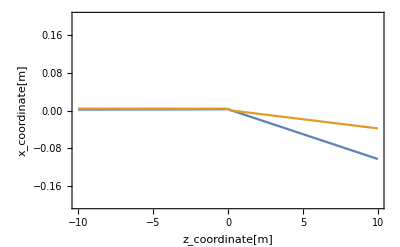

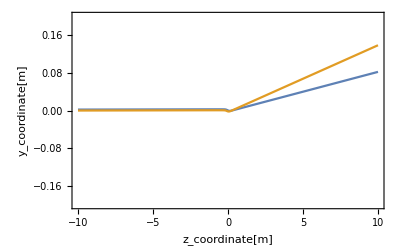

```mathematica
(*Orbit plot*)
Table[xy[i]=Table[{SOL[i][[1]][t],SOL[i][[2]][t]},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
Table[xz[i]=Table[{SOL[i][[3]][t],SOL[i][[1]][t]},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
Table[yz[i]=Table[{SOL[i][[3]][t],SOL[i][[2]][t]},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];

XY[1]=ListPlot[Table[xy[i],{i,1,2}],PlotRange->{{-0.03,0.03},{-0.03,0.03}},FrameLabel->{"x_coordinate[m]","y_coordinate[m]"},AspectRatio->1,LabelStyle->Directive[15],PlotStyle->PointSize[0.009],Joined->True,Frame->True]

XZ[1]=ListPlot[Table[xz[i],{i,1,2}],PlotRange->{{-10,10},{-0.2,0.2}},FrameLabel->{"z_coordinate[m]","x_coordinate[m]"},LabelStyle->Directive[15],PlotStyle->PointSize[0.009],Joined->True,Frame->True]

YZ[1]=ListPlot[Table[yz[i],{i,1,2}],PlotRange->{{-10,10},{-0.2,0.2}},FrameLabel->{"z_coordinate[m]","y_coordinate[m]"},LabelStyle->Directive[15],PlotStyle->PointSize[0.009],Joined->True,Frame->True]
```

```mathematica
$HistoryLength=3;
Timing[Aθ[r_,z_]:=NIntegrate[(R^2*r)/(2π)((Sin[θ]*Sin[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ])))/(Bz0),{θ,0,2π}];
Table[Invari[i]=Table[{SOL[i][[3]][t],m*γ*(SOL[i][[1]][t]*SOL[i][[2]]'[t]-SOL[i][[2]][t]*SOL[i][[1]]'[t])+Inum*q*Aθ[√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2),SOL[i][[3]][t]]*√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
(*P_sita vs z*)

Table[MAM[i]=Table[{SOL[i][[3]][t],m*γ*(SOL[i][[1]][t]*SOL[i][[2]]'[t]-SOL[i][[2]][t]*SOL[i][[1]]'[t])},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
(*Mechanical_Anguler_momentum vs z*)

Table[PT[i]=Table[{SOL[i][[3]][t],Inum*q*Aθ[√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2),SOL[i][[3]][t]]*√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
(*Potential term vs z*)

Table[Gamma3d[i]=Table[{SOL[i][[3]][t],1/√(1-(SOL[i][[1]]'[t]^2+SOL[i][[2]]'[t]^2+SOL[i][[3]]'[t]^2)/clight^2)},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
Table[Beta3d[i]=Table[{SOL[i][[3]][t],√(SOL[i][[1]]'[t]^2+SOL[i][[2]]'[t]^2+SOL[i][[3]]'[t]^2)/clight},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
Table[Gammaz[i]=Table[{SOL[i][[3]][t],1/√(1-(SOL[i][[3]]'[t]^2)/clight^2)},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
Table[Betaz[i]=Table[{SOL[i][[3]][t],SOL[i][[3]]'[t]/clight},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
(*Beta and gamma vs z*)

Table[Rorb[i]=Table[{SOL[i][[3]][t],√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
(*r vs z*)

Table[Rdorb[i]=Table[{SOL[i][[3]][t],((SOL[i][[1]][t]*SOL[i][[1]]'[t]+SOL[i][[2]][t]*SOL[i][[2]]'[t])/(√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2))*1/(SOL[i][[3]]'[t]))},{t,0,Lz/v,Lz/v/2000}],{i,1,2}];
(*rd vs z*)
]
```

{74.51753,Null}

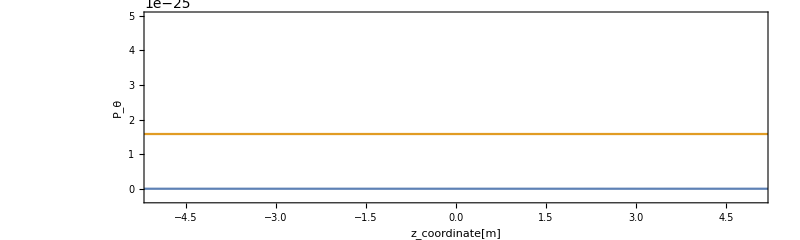

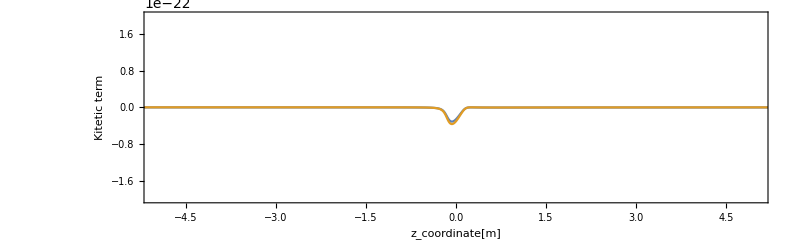

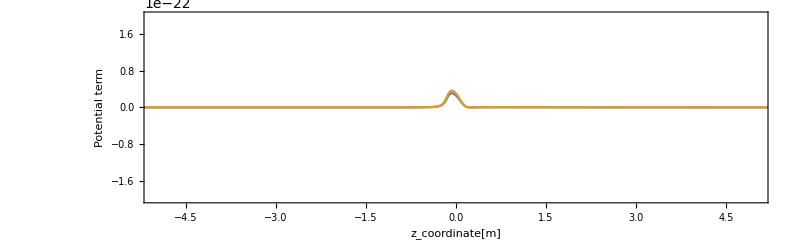

```mathematica
(*Plot of P_sita, Kinetic term and Potential term*)
Ps[1]=ListPlot[Table[Invari[i],{i,1,2}],PlotRange->{{-5,5},{-0.3*10^-25,5*10^-25}},FrameLabel->{"z_coordinate[m]","P_θ"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
Kt[1]=ListPlot[Table[MAM[i],{i,1,2}],PlotRange->{{-5,5},{-2*10^-22,2*10^-22}},FrameLabel->{"z_coordinate[m]","Kitetic term"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
Pt[1]=ListPlot[Table[PT[i],{i,1,2}],PlotRange->{{-5,5},{-2*10^-22,2*10^-22}},FrameLabel->{"z_coordinate[m]","Potential term"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
```

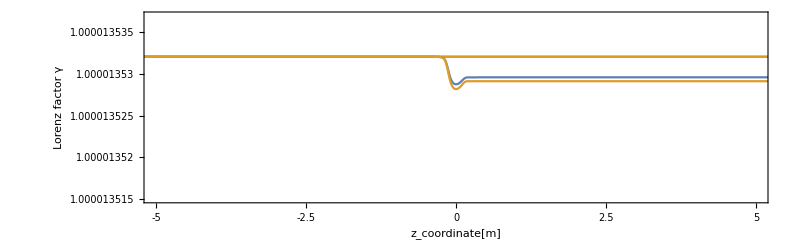

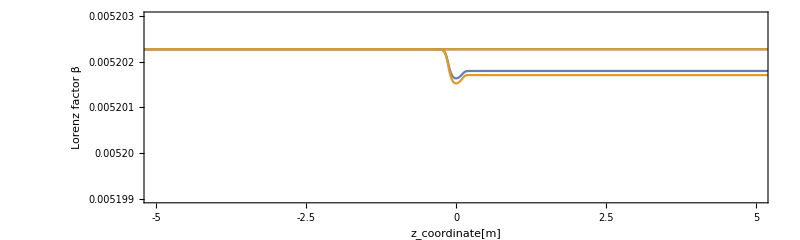

```mathematica
(*Plot of Lorentz factors inclue 3direction and z direction*)
LG[1]=Show[
ListPlot[Table[Gamma3d[i],{i,1,2}],PlotRange->{{-5,5},{1.000013515,1.000013537}},FrameTicks->{{{{1.000013515,"1.000013515"},{1.00001352,"1.00001352"},{1.000013525,"1.000013525"},{1.00001353,"1.00001353"},{1.000013535,"1.000013535"}},None},{{-5,-2.5,0,2.5,5},None}},FrameLabel->{"z_coordinate[m]","Lorenz factor γ"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}],
ListPlot[Table[Gammaz[i],{i,1,2}],PlotRange->{{-5,5},{1.0000135,1.0000136}},FrameTicks->{{{{1.0000135,"1.0000135"},{1.00001355,"1.00001355"},{1.0000136,"1.0000136"}},None},{{-5,-2.5,0,2.5,5},None}},FrameLabel->{"z_coordinate[m]","Lorenz factor γ"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
]
LB[1]=Show[
ListPlot[Table[Beta3d[i],{i,1,2}],PlotRange->{{-5,5},{0.005199,0.005203}},FrameTicks->{{{{0.005199,"0.005199"},{0.00520,"0.00520"},{0.005201,"0.005201"},{0.005202,"0.005202"},{0.005203,"0.005203"}},None},{{-5,-2.5,0,2.5,5},None}},FrameLabel->{"z_coordinate[m]","Lorenz factor β"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}],
ListPlot[Table[Betaz[i],{i,1,2}],PlotRange->{{-5,5},{0.00519,0.00521}},FrameLabel->{"z_coordinate[m]","Lorenz factor β_b"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
]
```

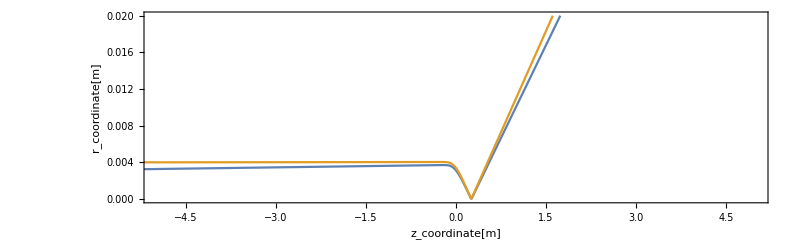

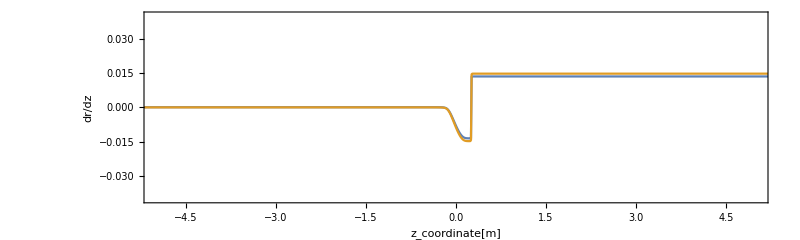

```mathematica
(*orbit plot of r and dr/dz*)
Ro[1]=ListPlot[Table[Rorb[i],{i,1,2}],PlotRange->{{-5,5},{0,2*10^-2}},FrameLabel->{"z_coordinate[m]","r_coordinate[m]"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
Rdo[1]=ListPlot[Table[Rdorb[i],{i,1,2}],PlotRange->{{-5,5},{-4*10^-2,4*10^-2}},FrameLabel->{"z_coordinate[m]","dr/dz"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,AspectRatio->0.3,ImageSize->{800,240}]
```

```mathematica
$HistoryLength=3;
Aθ[r_,z_]:=NIntegrate[(R^2*r)/(2π)((Sin[θ]*Sin[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ])))/(Bz0),{θ,0,2π}];

Table[RKick[i,t_]:=SOL[i][[3]]'[t]*((Inum*q*Bz[√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2),SOL[i][[3]][t]])/(m*γ)*(SOL[i][[1]][t]*SOL[i][[2]]'[t]-SOL[i][[2]][t]*SOL[i][[1]]'[t])/(√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)*SOL[i][[3]]'[t]^2)+1/((SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)^(3/2)*SOL[i][[3]]'[t]^2)*(-(SOL[i][[1]][t]*SOL[i][[1]]'[t]+SOL[i][[2]][t]*SOL[i][[2]]'[t])^2+(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)*(SOL[i][[1]]'[t]^2+SOL[i][[2]]'[t]^2))-(Inum*q*Br[√(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2),SOL[i][[3]][t]])/(m*γ*(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)*SOL[i][[3]]'[t]^3)*(SOL[i][[1]][t]*SOL[i][[1]]'[t]+SOL[i][[2]][t]*SOL[i][[2]]'[t])*(SOL[i][[2]][t]*SOL[i][[1]]'[t]-SOL[i][[1]][t]*SOL[i][[2]]'[t])-((m*γ*(SOL[i][[1]][0]*SOL[i][[2]]'[0]-SOL[i][[2]][0]*SOL[i][[1]]'[0])+Inum*q*Aθ[√(SOL[i][[1]][0]^2+SOL[i][[2]][0]^2),SOL[i][[3]][0]]*√(SOL[i][[1]][0]^2+SOL[i][[2]][0]^2))/(m*γ*v))^2/(SOL[i][[1]][t]^2+SOL[i][[2]][t]^2)^(3/2)),{i,1,2}];

Timing[Table[RDD[i]=NIntegrate[RKick[i,t],{t,0,Lz/v}],{i,1,2}];
]
```

{269.54258,Null}

```mathematica
ClearAll[r0];
Bz00[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));(*Bz field*)
Bz1[z_]:=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz00[0];(*Scaled Bz field*)
Bz2[z_]:=Bz1'[z];(*Scaled Bz field*)
Bz3[z_]:=Bz2'[z];(*Scaled Bz field*)
Bz4[z_]:=Bz3'[z];(*Scaled Bz field*)
Bz5[z_]:=Bz4'[z];(*Scaled Bz field*)
Bz6[z_]:=Bz5'[z];(*Scaled Bz field*)
Brho=m*γ*v/(Inum*q);
r0[1]=Table[√(Xinit[1][[i]]^2+Yinit[1][[i]]^2),{i,1,2}];
Timing[
Table[RD1[i]=-1/4*NIntegrate[(Bz1[z]/Brho)^2*r0[1][[i]],{z,-∞,∞}],{i,1,2}];
Table[RD2[i]=-1/8*NIntegrate[(Bz2[z]/Brho)^2*r0[1][[i]]^3,{z,-∞,∞}],{i,1,2}];
Table[RD3[i]=-5/256*NIntegrate[(Bz3[z]/Brho)^2*r0[1][[i]]^5,{z,-∞,∞}],{i,1,2}];
Table[RD4[i]=-7/4608*NIntegrate[(Bz4[z]/Brho)^2*r0[1][[i]]^7,{z,-∞,∞}],{i,1,2}];
Table[RD5[i]=-7/98304*NIntegrate[(Bz5[z]/Brho)^2*r0[1][[i]]^9,{z,-∞,∞}],{i,1,2}];
]
```

{0.19221,Null}

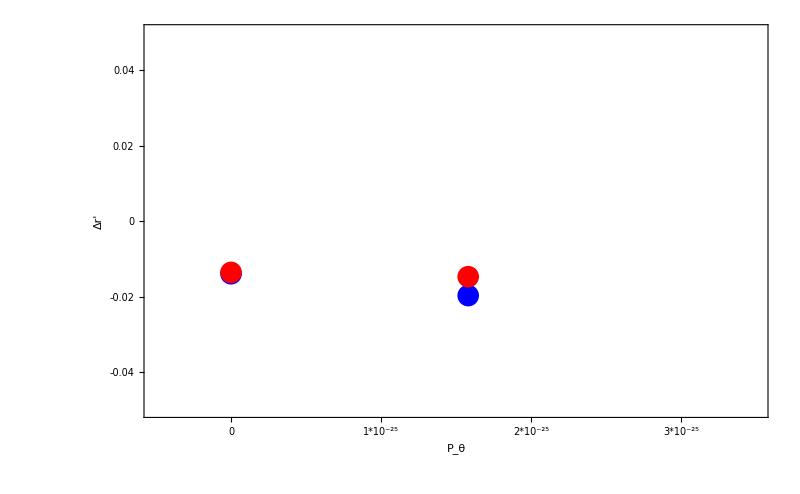

```mathematica
Rdd[1]=Show[
ListPlot[Table[{Invari[i][[1,2]],(RD1[i]+RD2[i]+RD3[i]+RD4[i]+RD5[i])},{i,1,2}],PlotRange->{{-0.5*10^-25,3.5*10^-25},{-0.05,0.05}},FrameTicks->{{{{-0.04,"-0.04"},{-0.02,"-0.02"},{0,"0"},{0.02,"0.02"},{0.04,"0.04"}},None},{{{0,"0"},{1*10^-25,"1*10^-25"},{2*10^-25,"2*10^-25"},{3*10^-25,"3*10^-25"}},None}},PlotStyle->{Blue},FrameLabel->{"P_θ","Δr'"},LabelStyle->Directive[15],Frame->True,Axes->None],
ListPlot[Table[{Invari[j][[1,2]],RDD[j]},{j,1,2}],PlotRange->{{-0.5*10^-25,3.5*10^-25},{-0.05,0.05}},PlotStyle->{Red},FrameLabel->{"P_θ","Δr'"},LabelStyle->Directive[15],Frame->True,Axes->None]
]
```